```mathematica
phi[x_,y_]:=1/(√(x^2+y^2))
```

```mathematica
phiTotal[x_,y_]=phi[x-l,y]-phi[x+l,y]
```

1/(√((-l+x)^2+y^2))-1/(√((l+x)^2+y^2))

```mathematica
EField=D[-phiTotal[x,y],{{x,y}}]
```

{(-l+x)/(((-l+x)^2+y^2)^(3/2))-(l+x)/(((l+x)^2+y^2)^(3/2)),y/(((-l+x)^2+y^2)^(3/2))-y/(((l+x)^2+y^2)^(3/2))}

```mathematica
l=1/4;
```

```mathematica
colorFunction=Function[{z},Blend[{Blue,White,Red},z]];
```

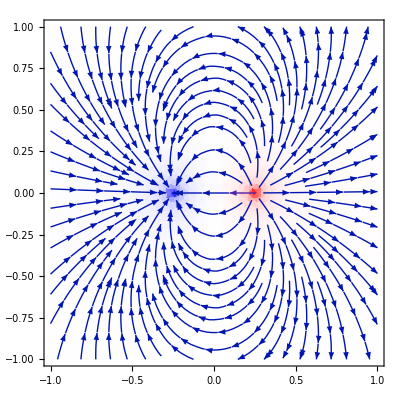

```mathematica
Show@{

DensityPlot[
phiTotal[x,y],{x,-1,1},{y,-1,1},
ColorFunction->colorFunction,
PlotRange->Full,
AspectRatio->Automatic,
PlotPoints->20
],

StreamPlot[
EField,{x,-1,1},{y,-1,1}
]

}
```